(I start off every notebook with these two commands to clear the namespace and anchor the directory)

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

# The Best Way to Bucket the Alphabet

Let’s divide up the alphabet to get equal numbers of Americans in each bucket

```mathematica
percents = CloudGet["https://www.wolframcloud.com/objects/e338adb3-f090-4867-8456-f3f66c422f38"]
```

<|A→0.0379425,B→0.0850223,C→0.077475,D→0.0453413,E→0.0185658,F→0.0338085,G→0.0557632,H→0.0708041,I→0.00413011,J→0.0298697,K→0.0326326,L→0.0491037,M→0.0963997,N→0.0190822,O→0.0152516,P→0.0498137,Q→0.00241787,R→0.0590957,S→0.0943162,T→0.0354322,U→0.00232247,V→0.0175313,W→0.0554885,X→0.000384696,Y→0.00634222,Z→0.00566274|>

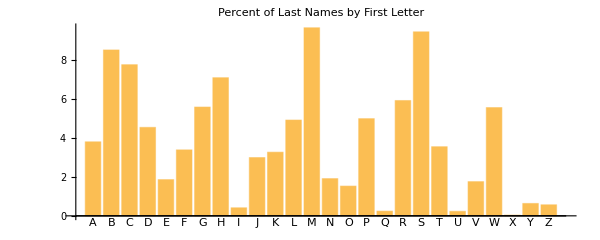

```mathematica
BarChart[100. * percents, ChartLabels->Keys@percents,
	PlotLabel->Style["Percent of Last Names by First Letter", FontSize->14, Black, Bold],
	ImageSize->600,
	AspectRatio->0.4
]
```

### Arranging names the usual way

Image there are N tables with ID badges for thousands of people, arranged by last name.

An obvious way is to arrange the letters into 4 ranges of lengths 6, 7, 6 and 7 (A-F, G-M, N-S, T-Z). Let’s see what those lines will look like. Ideally, each would have around 0.25

```mathematica
alphabet = Keys@percents;
```

Looking ahead, let’s assume any number of spans as an array `sizes_`, like {6,7,6,7} or {5,5,5,5,6}

```mathematica
getLetterGroups[sizes_] := (
	starts = Most@FoldList[Plus, 1, sizes];
	ends = Rest@FoldList[Plus, 0, sizes];
	ranges = Transpose[{starts, ends}];
	groups = Take[alphabet, { First@#, Last@# }]& /@ ranges
)
getLetterGroups[{6,7,6,7}]
```

{{A,B,C,D,E,F},{G,H,I,J,K,L,M},{N,O,P,Q,R,S},{T,U,V,W,X,Y,Z}}

```mathematica
getLineLengths[sizes_] := (
	letterGroups = getLetterGroups[sizes];
	values = Map[AssociationThread[#, percents[#]& /@ #]&, letterGroups];
	spans = <| 
		"label" -> First@Keys@# <> "-" <> Last@Keys@#,
		"total" -> Total@#,
		"values" -> #
	|>& /@ values
)
```

```mathematica
chartLines[groups_] := (
	labels = #["label"]& /@ groups;
	totals = 100. * #["total"]& /@ groups;
	span = Max@totals - Min@totals;
	BarChart[
		#["values"]& /@ groups,
		ChartLabels->{ Placed[{labels, (ToString[Round[#,0.01]] <> "%")& /@ totals}, {Bottom, Top}], None},
		ChartLayout->"Stacked",
		PlotLabel->Style["Range of " <> ToString[Round[span, 0.01]] <> " percentage points", FontSize->14, Bold]
	]
)
```

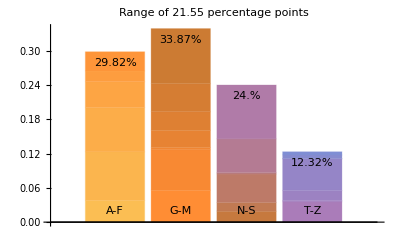

```mathematica
groupsTypical = getLineLengths[{6, 7, 6, 7 }];
chartLines[groupsTypical]
```

That’s no good! Just for fun, let’s visualize what this looks like if 250 people get in line

```mathematica
drawLines[groupsTypical_] := (
	Graphics[
		Flatten@Table[(
			people = Round[groupsTypical[[Length@groupsTypical + 1 - t]]["total"] * 250];
			Prepend[
				Table[Disk[{4*x + 8, t * 12}, 1.6], {x, 1, people }],
				Text[Style[groupsTypical[[Length@groupsTypical + 1 - t]]["label"], FontSize->13, Bold, Red], {0, t * 12}]
			]
		), {t, 1, Length@groupsTypical}],
		ImageSize->700
	]
)
```

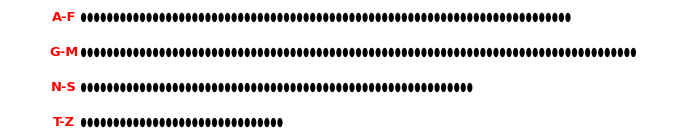

```mathematica
drawLines[groupsTypical]
```

Would five table be better?

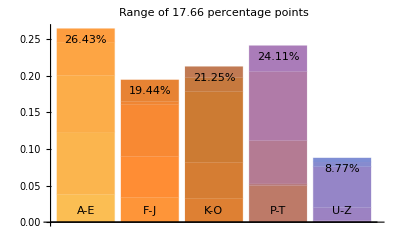

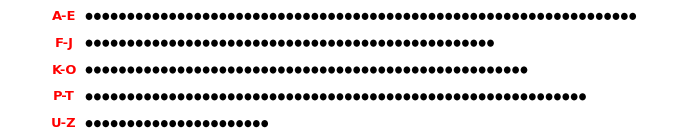

```mathematica
groupsTypical5 = getLineLengths[{5, 5, 5, 5, 6 }];
chartLines[groupsTypical5]
drawLines[groupsTypical5]
```

Hmm, not much better

### Okay, so what’s the optimal split?

Let’s start with the cumulative percentage is through the alphabet

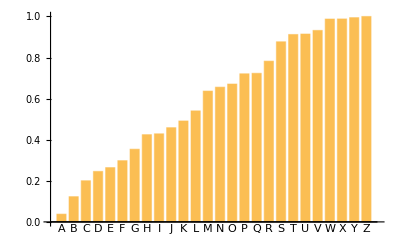

```mathematica
cumulative = Rest@FoldList[Plus, 0, Values@percents];
BarChart[cumulative, ChartLabels->alphabet]
```

We can use this to identify where the cumulative percentages are the closest to rounding to a multiple of the target percentage

```mathematica
findOptimal[numberOfGroups_] := (
	cumulative = Rest@FoldList[Plus, 0, Values@percents];
	distanceFromIdeal = Mod[#, 1 / numberOfGroups]& /@ cumulative;
	(* locate the cutoffs *)
	cutoffs = Most@distanceFromIdeal - Rest@distanceFromIdeal;
	indices = Prepend[Flatten@Position[cutoffs, _?(# > 0 &)], 0];
	groupSizes = Rest@indices - Most@indices;
	Append[groupSizes, 26 - Total@groupSizes]
)
```

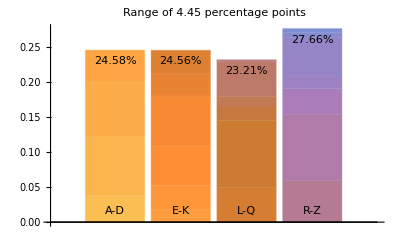

```mathematica
optimal4 = findOptimal[4];
groupsOptimal4 = getLineLengths[optimal4];
chartLines[groupsOptimal4]
```

What if we squeezed in a fifth table?

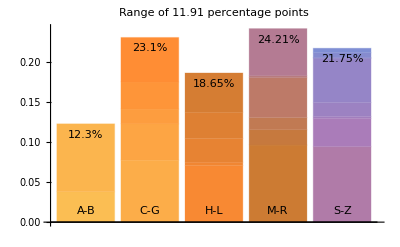

```mathematica
optimal5 = findOptimal[5];
groupsOptimal5 = getLineLengths[optimal5];
chartLines[groupsOptimal5]
```

Even worse! Three tables?

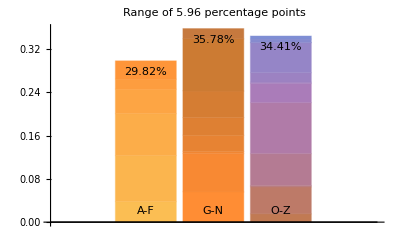

```mathematica
optimal3 = findOptimal[3];
groupsOptimal3 = getLineLengths[optimal3];
chartLines[groupsOptimal3]
```

Okay, so four tables is best, but it’s still onerous on those of us in R-Z. We can do better! See next notebook.